0

6

1

1

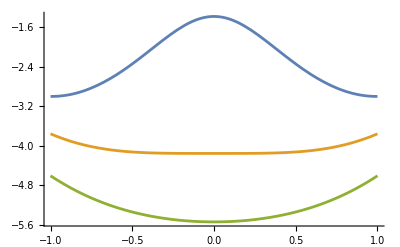

```mathematica
(*2c*)
B = 0
q = 6
J = 1
k = 1
a[B_,m_,T_]:=q J m^2/2-k T Log[2 Cosh[(B+q J m)/(k T)]];
(* As we saw before, kT = qJ, so in reduced units the critical temp is qJ/k = 6*)
Plot[{a[0, m, 2], a[0, m, 6], a[0, m, 8]}, {m, -1, 1}]
```

```mathematica
(*2d:*)

(*This version of the Ising Model still has "that transcendental equation for m", namely m = tanh[(β(B + q J m))]

Thankfully we can solve the above for B*)

Bsol[m_, T_]:= k T ArcTanh[m] - q J m
```

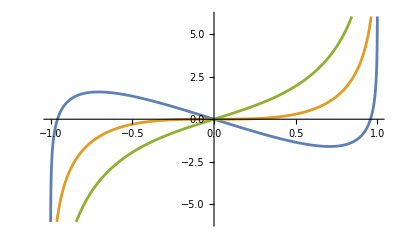

```mathematica
Plot[{Bsol[m, 3], Bsol[m, 6], Bsol[m, 9]}, {m, -1, 1}]
```

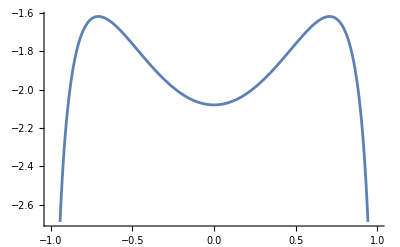

```mathematica
(* The number of crossings in the above B-m plot indicates the number of solutions we have for criticality in our free energy. Three solutions (one unstable) for T< Tc, else one solution *)

(*2e *)
Plot[a[Bsol[m, 3], m, 3], {m, -1, 1}]
```

```mathematica
(*The bistable region is between the two "humps". In an equilibrium process, this will collapse to one of two phases. *)

(*3c *)
P[ρ_, T_] := -ϵ  q  ρ^2 +  k T Log[1/(1-ρ)]
μ[ρ_, T_] := -2 ϵ q ρ + k T Log[(ρ )/ (1 -ρ)]

Solve[{D[P[ρ, T], ρ] ==0, D[P[ρ, T], {ρ, 2}] == 0}, {ρ, T}]
```

{{ρ→1/2,T→(q ϵ)/(2 k)}}

6

1

1

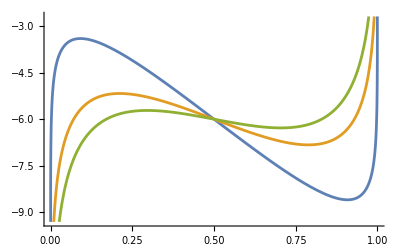

```mathematica
(*3d: i *)
q = 6
k = 1
ϵ = 1

Plot[{μ[ρ, 1], μ[ρ, 2],  μ[ρ, 2.5]}, {ρ, 0, 1}]
```

```mathematica
(*3d: ii*)
```

```mathematica
μcrit = μ[1/2, 3]
```

-6

```mathematica
ρsol[T_, ρguess_]:= FindRoot[μ[ρ, T] == μcrit, {ρ, ρguess}][[1,2]]
(* 3d: iii*)
```

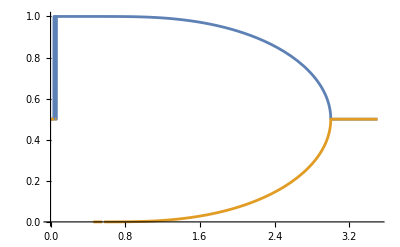

```mathematica
Plot[{ρsol[T, 0.999], ρsol[T, 0.001]}, {T, 0, 3.5}]
```

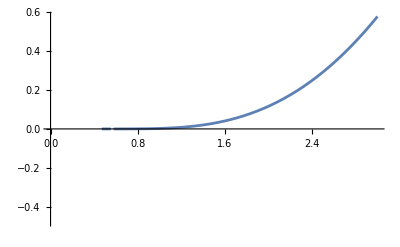

```mathematica
(*3d: iv*)
Plot[{P[ρsol[T, 0.999], T]}, {T, 0, 3}]
```

```mathematica
(*# 1*)
Integrate[1/r^a, {r, k, N - n + k -1}]
(*Integrate[Integrate[1/r^a, {r, k, N - n + k -1}], {k, 1, n}]*)
```

ConditionalExpression[((-n+N)^-a (n-N+(-n+N)^a))/(-1+a), Re[n]<Re[N]||-n+N∉ℝ]

ConditionalExpression[((-n+N)^-a (n-N+(-n+N)^a))/(-1+a), Re[n]<Re[N]||-n+N∉ℝ]

ConditionalExpression[(k^(1-a)-(-1+k-n+N)^(1-a))/(-1+a), (k/(1+n-N)≠0&&Re[k/(1+n-N)]≤0&&((Re[k]==0&&((1+Re[n]==Re[N]&&((Im[k]<0&&Im[n]>Im[N]&&Im[k]+Im[N] Re[k]+Im[k] Re[n]≤Im[n] Re[k]+Im[k] Re[N])||(Im[k]>0&&Im[n]<Im[N]&&Im[k]+Im[N] Re[k]+Im[k] Re[n]≥Im[n] Re[k]+Im[k] Re[N])))||(Im[k]<0&&Im[n]≥Im[N]&&(1+Re[n]<Re[N]||(1+Re[n]>Re[N]&&Im[k]+Im[N] Re[k]+Im[k] Re[n]≤Im[n] Re[k]+Im[k] Re[N])))||(Im[k]>0&&Im[n]≤Im[N]&&(1+Re[n]<Re[N]||(1+Re[n]>Re[N]&&Im[k]+Im[N] Re[k]+Im[k] Re[n]≥Im[n] Re[k]+Im[k] Re[N])))))||(Im[n]<Im[N]&&((Re[k]>0&&((Im[k]≥0&&(1+Re[n]<Re[N]||Im[k] Im[n]+Re[k]+Re[k] Re[n]≤Im[k] Im[N]+Re[k] Re[N]))||(Im[k] Im[n]+Re[k]+Re[k] Re[n]≤Im[k] Im[N]+Re[k] Re[N]&&((1+Re[n]≥Re[N]&&Im[k]+Im[N]≤Im[n])||Im[k]+Im[N] Re[k]+Im[k] Re[n]≥Im[n] Re[k]+Im[k] Re[N]))))||(Im[k]+Im[N]≤Im[n]&&Re[k]≥0&&1+Re[n]<Re[N]&&Im[k] Im[n]+Re[k]+Re[k] Re[n]≤Im[k] Im[N]+Re[k] Re[N])))||(Im[n]>Im[N]&&((Im[k] Im[n]+Re[k]+Re[k] Re[n]≤Im[k] Im[N]+Re[k] Re[N]&&((Im[k]+Im[N]≥Im[n]&&(Re[k]≥0||1+Re[n]≥Re[N])&&(1+Re[n]<Re[N]||Re[k]>0))||(Re[k]>0&&(Im[k]≤0||Im[k]+Im[N] Re[k]+Im[k] Re[n]≤Im[n] Re[k]+Im[k] Re[N]))))||(Im[k]≤0&&Re[k]>0&&1+Re[n]<Re[N])))))||(Re[k]≥0&&((k/(1+n-N)∉ℝ&&((1+Re[n]==Re[N]&&Im[k]/(Im[n]-Im[N])≥1)||(Im[n]≤Im[N]&&(Im[k]≥0||Im[k]+Im[N] Re[k]+Im[k] Re[n]≥Im[n] Re[k]+Im[k] Re[N]))||(Im[n]<Im[N]&&Im[k]+Im[N]≤Im[n])||(Im[n]≥Im[N]&&(Im[k]≤0||Im[k]+Im[N] Re[k]+Im[k] Re[n]≤Im[n] Re[k]+Im[k] Re[N]))||(Im[k]+Im[N]≥Im[n]&&Im[n]>Im[N])))||(Re[k/(1+n-N)]>1&&((Im[n]≤Im[N]&&(Im[k]≥0||Im[k]+Im[N] Re[k]+Im[k] Re[n]≥Im[n] Re[k]+Im[k] Re[N]))||(Im[n]<Im[N]&&Im[k]+Im[N]≤Im[n])||(Im[n]≥Im[N]&&(Im[k]≤0||Im[k]+Im[N] Re[k]+Im[k] Re[n]≤Im[n] Re[k]+Im[k] Re[N]))||(Im[n]>Im[N]&&Im[k]+Im[N]≥Im[n])))))]

```mathematica
Integrate[(k^(1-a)-(-1+k-n+N)^(1-a))/(-1+a), {k, 1, n}]
```